```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;rep={kx-> k Sin[θ] Cos[ϕ],ky-> k Sin[θ]Sin[ϕ],kp-> k Sin[θ],kz-> k Cos[θ], ξ^2->1};
ass=Assumptions->{en,k,θ,ϕ,kx,ky,kz,κr,κi,kw,k1,k2}∈ Reals &&  k>0 && kp>0 && en>=0 && v>0 && vz>0 && kw>0;
sx=({{0, 1}, {1, 0}});sy=({{0, -ⅈ}, {ⅈ, 0}});sz=({{1, 0}, {0, -1}});
id=({{1, 0}, {0, 1}});ene=1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2);
```

## quad Weyl node

```mathematica
Clear[ham,eval,dx,dy,dz,v];
(* -Graphics-; PRB B 106,134108 (2022) *)
{dx,dy,dz}={ ((*√3*)v(kx^2-ky^2))/2,(kx^2+ky^2-2 kz^2)/2,(*√3*)v kx ky kz};
ham=dx sx+dy sy+dz sz;
{ev,vec}=FullSimplify[Eigensystem[ham],ass]
```

{{-1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2),1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)},{{-(ⅈ (-2 kx ky kz v+√((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)))/(2 kz^2+ky^2 (-1-ⅈ v)+ⅈ kx^2 (ⅈ+v)),1},{(ⅈ (2 kx ky kz v+√((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)))/(2 kz^2+ky^2 (-1-ⅈ v)+ⅈ kx^2 (ⅈ+v)),1}}}

```mathematica
{ (√3(kx^2-ky^2))/2,(kx^2+ky^2-2 kz^2)/2,√3 kx ky kz}/.{kx->k1+k2,ky->k1-k2}//FullSimplify
```

{2 √3 k1 k2,k1^2+k2^2-kz^2,√3 (k1-k2) (k1+k2) kz}

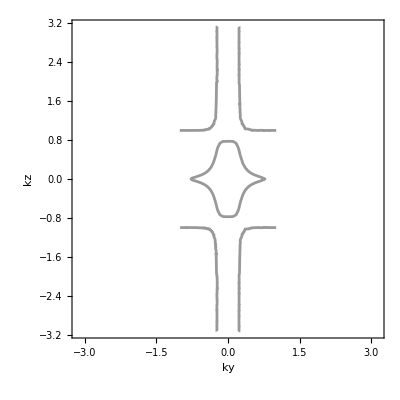

```mathematica
lim=π;kx=(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2));v=20;ContourPlot[ene==0.6,{ky,-lim,lim},{kz,-lim,lim},AxesLabel->{ky,kz},Mesh->None,ContourStyle->{Directive[Blue,Opacity[0.5]],Directive[Green,Opacity[0.4]],Directive[Gray,Opacity[0.8]]},RegionFunction->Function[{ky,kz,z},-ky^2+2 kz^2+ky^2 -2 ky^2 kz^2 >=0]]
Clear[kx,v];
```

```mathematica
eqq=1/2 √((kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2)) v^2)/.{ky->0,kz->0}
Solve[eqq==μ,kx]
```

1/2 √(kx^4+kx^4 v^2)

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{kx→-(√2 √μ)/((1+v^2)^(1/4))},{kx→-(ⅈ √2 √μ)/((1+v^2)^(1/4))},{kx→(ⅈ √2 √μ)/((1+v^2)^(1/4))},{kx→(√2 √μ)/((1+v^2)^(1/4))}}

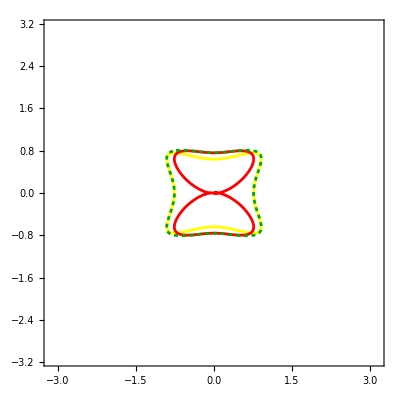

```mathematica
mu=0.41;v=1;kx=0;c1=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2))==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Yellow];
kx=mu/2;c2=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2))==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Cyan];
kx=mu;c3=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2))==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Pink];
kx=2^(1/4) √mu;
c4=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2))==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Red];
kx=(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2));
c5=ContourPlot[(kx^2+ky^2-2 kz^2)^2+(kx^4+ky^4+2 kx^2 ky^2 (-1+2 kz^2))==4mu^2,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Directive[Darker[Green],Dashing[0.007]],RegionFunction->Function[{ky,kz,z},Chop[-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2]>=0]];
Show[c1,c4,c5]
```

```mathematica
lim=π;v=1;mu=0.25;(*ContourPlot3D[{ene==mu,kx==0,kx==ky},{kx,-lim,lim},{ky,-lim,lim},{kz,-lim,lim},AxesLabel->{kx,ky,kz},Mesh->None,ContourStyle->{Directive[Blue,Opacity[0.5]],Directive[Green,Opacity[0.4]],Directive[Gray,Opacity[0.8]]}]*)
fs1=ContourPlot3D[{(*ene==μ,*)kx==(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2)) },{kx,-1,1},{ky,-1,1},{kz,-1,1},Mesh->None,ContourStyle->Directive[Lighter[Yellow],Opacity[0.5]]];
fs=ContourPlot3D[{ene==mu(*,kx==0*)},{kx,-1,1},{ky,-1,1},{kz,-1,1},ContourStyle->Directive[Darker[Blue],Opacity[0.5] ],Ticks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"}];
(*********)
plt=Show[fs,fs1,Ticks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},AxesLabel->{"k_x","k_y","k_z"},ImageSize->350,(***)ViewCenter->{{0.5,0.5,0.5},{0.5,0.5}},ViewMatrix->{{{-0.02229479690635771,0.21908986983455608,0.4265003762797671,2.00744472288256*^-17},{0.4616131047187078,-0.10566565842790686,0.07840988573485642,-1.0919234502718313*^-16},{-0.12967761403904926,-0.4138047819502262,0.2057895013169175,2.144855903328518},{0.,0.,0.,1.}},{{1.8885620632287061,0.,0.5,0.},{0.,1.8885620632287063,0.5,0.},{0.,0.,2.748083405500971,-5.113751355433945},{0.,0.,1.,0.}}},ViewPoint->{0.5794579083358568,1.8490658945656515,-0.919560055713793},ViewProjection->"\"Perspective\"",ViewRange->{2.842425715905351,6.0944738812968176},ViewVector->{{1.207203975699702,3.8522206136784405,-1.9157501160704022},{0.,0.,0.}},ViewVertical->{0.9616939681639723,-0.22013678839147321,0.16335392861428338},ImagePadding->{{30, 30}, {30, 30}}]
Clear[v];
SetDirectory[NotebookDirectory[]];
Export["qWeyl-fs.pdf",Rasterize[plt],ImageResolution->100];
```

-Graphics3D-

```mathematica
AbsoluteOptions[]
```

```mathematica
lim=π;v=1;mu=0.25;th=0.007;
fs1=ContourPlot3D[{kx==(√(-ky^2+2 kz^2+ky^2 v^2-2 ky^2 kz^2 v^2))/(√(1+v^2)) },{kx,-1,1},{ky,-1,1},{kz,-1,1},Mesh->None,ContourStyle->Directive[(*RGBColor[{0,0.2,1}]*)Yellow,Opacity[0.5]]];
fs=ContourPlot3D[{ene==mu},{kx,-1,1},{ky,-1,1},{kz,-1,1},ContourStyle->Directive[Lighter[Pink],Opacity[0.6] ],Ticks->None,LabelStyle->{Black,Bold,22,FontFamily->"TexMaths Symbols"},(**)MeshStyle->{Directive[Darker[Brown],Thickness[0.005]],Directive[Darker[Purple],Thickness[th]]}];
(*********)
plt=Show[fs,fs1,Ticks->None,LabelStyle->{Black,Bold,24,FontFamily->"TexMaths Symbols"},AxesLabel->{"k_x","k_y","k_z"},ImageSize->350,(***)ViewCenter->{{0.5,0.5,0.5},{0.5,0.5}},ViewMatrix->{{{-0.02229479690635771,0.21908986983455608,0.4265003762797671,2.00744472288256*^-17},{0.4616131047187078,-0.10566565842790686,0.07840988573485642,-1.0919234502718313*^-16},{-0.12967761403904926,-0.4138047819502262,0.2057895013169175,2.144855903328518},{0.,0.,0.,1.}},{{1.8885620632287061,0.,0.5,0.},{0.,1.8885620632287063,0.5,0.},{0.,0.,2.748083405500971,-5.113751355433945},{0.,0.,1.,0.}}},ViewPoint->{0.5794579083358568,1.8490658945656515,-0.919560055713793},ViewProjection->"\"Perspective\"",ViewRange->{2.842425715905351,6.0944738812968176},ViewVector->{{1.207203975699702,3.8522206136784405,-1.9157501160704022},{0.,0.,0.}},ViewVertical->{0.9616939681639723,-0.22013678839147321,0.16335392861428338},ImagePadding->{{30, 30}, {30, 30}}]
Clear[v];
SetDirectory[NotebookDirectory[]];
Export["qWeyl-prl.pdf",Rasterize[plt],ImageResolution->100];
```

-Graphics3D-

```mathematica
Solve[kx==k1+k2 && ky==k1-k2,{k1,k2}]
```

{{k1→(kx+ky)/2,k2→(kx-ky)/2}}

```mathematica
eqq=kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2));
FullSimplify[Solve[eqq==0,ky],ass]
```

{{ky→-(√(kz^2+kx^2 (1-3 kz^2)-√(-3 kz^4-6 kx^2 kz^2 (-1+kz^2)+kx^4 (-3-6 kz^2+9 kz^4))))/(√2)},{ky→(√(kz^2+kx^2 (1-3 kz^2)-√(-3 kz^4-6 kx^2 kz^2 (-1+kz^2)+kx^4 (-3-6 kz^2+9 kz^4))))/(√2)},{ky→-(√(kz^2+kx^2 (1-3 kz^2)+√(-3 kz^4-6 kx^2 kz^2 (-1+kz^2)+kx^4 (-3-6 kz^2+9 kz^4))))/(√2)},{ky→(√(kz^2+kx^2 (1-3 kz^2)+√(-3 kz^4-6 kx^2 kz^2 (-1+kz^2)+kx^4 (-3-6 kz^2+9 kz^4))))/(√2)}}

```mathematica
kz^2+kx^2 (1-3 kz^2)+√(-3 kz^4-6 kx^2 kz^2 (-1+kz^2)+kx^4 (-3-6 kz^2+9 kz^4))/.{kz->1(*/√3*), kx->1}//FullSimplify
```

-1+ⅈ √3

### Berry curvature

```mathematica
(*-Graphics-*)
ene=√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)));
Om=3/2{(kx^3(ky^2+kz^2))/ene^3,(ky^3(kx^2+ky^2))/ene^3,(kz^3(ky^2+kx^2))/ene^3};
VectorPlot3D[Om,{kx,-1,1},{ky,-1,1},{kz,-1,1},AxesLabel->{kx,ky,kz},Mesh->None]
kz=0;
VectorPlot[3/2{(kx^3(ky^2+kz^2))/ene^3,(ky^3(kx^2+ky^2))/ene^3},{kx,-1,1},{ky,-1,1}]
Clear[kz];
```

```mathematica
SliceVectorPlot3D[Om,{ky==0},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
SliceVectorPlot3D[Om,{"XStackedPlanes",1},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
SliceVectorPlot3D[Om,{"CenterCutSphere",π/2},{kx,-1,1},{ky,-1,1},{kz,-1,1},ScalingFunctions->None]
```

### dispersion analysis

```mathematica
lim=π;kz=0;
Plot3D[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))),-√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{kx,-lim,lim},{ky,-lim,lim},Mesh->None,AxesLabel->{kx,ky}]
ContourPlot[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{kx,-lim,lim},{ky,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},Contours->14];
Clear[kz];
(**********)
lim=π;ky=0;
Plot3D[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))),-√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{kx,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},AxesLabel->{kx,kz}]
ContourPlot[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{kx,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},Contours->14,PlotLegends->Automatic]
Clear[ky];
lim=π;kx=0;
Plot3D[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))),-√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{ky,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},AxesLabel->{ky,kz}]
ContourPlot[{√(kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2)))},{ky,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.5, 0.5, 0.7},Contours->14];
Clear[kx];
```

-Graphics3D-

## Rotating the coord sys to align along (1,1,1)

```mathematica
{ (√3(kx^2-ky^2))/2,(kx^2+ky^2-2 kz^2)/2,√3 kx ky kz}/.{kx->k1+k2,ky->k1-k2}//FullSimplify
```

{2 √3 k1 k2,k1^2+k2^2-kz^2,√3 (k1-k2) (k1+k2) kz}

```mathematica
{ddx,ddy,ddz}={2 √3 k1 k2,k1^2+k2^2-kz^2,√3 (k1-k2) (k1+k2) kz};
hamm=ddx sx+ddy sy+ddz sz;
FullSimplify[Eigenvalues[hamm],ass]
```

{-√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4),√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)}

### dispersion analysis2

-Graphics3D-

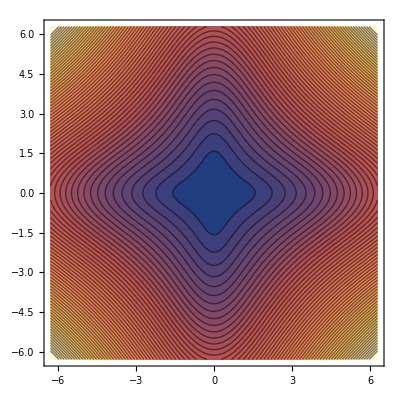

-Graphics3D-

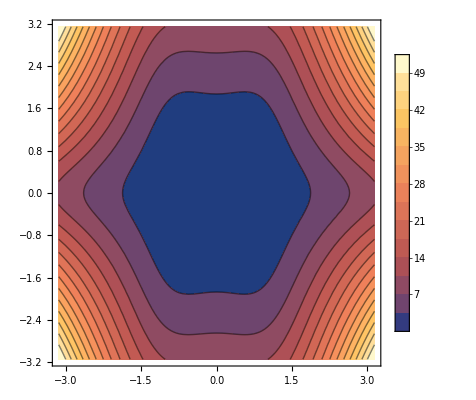

-Graphics3D-

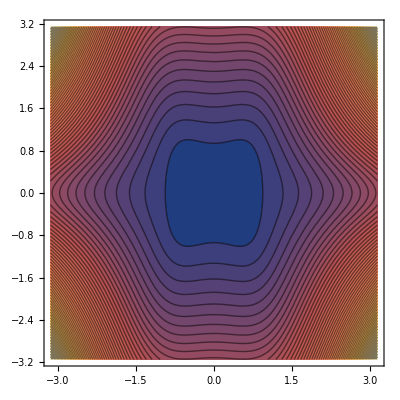

```mathematica
lim=2π;kz=0;
Plot3D[{-√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4),√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k1,-lim,lim},{k2,-lim,lim},Mesh->None,AxesLabel->{kx,ky}]
ContourPlot[{√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k1,-lim,lim},{k2,-lim,lim},Contours->60,Mesh->None,BoxRatios->{0.75, 0.75, 1},Contours->14]
Clear[kz];
(**********)
lim=π;k2=0;
Plot3D[{√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4),-√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k1,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},AxesLabel->{kx,kz}]
ContourPlot[{√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k1,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},Contours->14,PlotLegends->Automatic]
Clear[k2];
lim=π;k1=0;
Plot3D[{√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4),-√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k2,-lim,lim},{kz,-lim,lim},Mesh->None,BoxRatios->{0.75, 0.75, 1},AxesLabel->{ky,kz}]
ContourPlot[{√(k1^4+14 k1^2 k2^2+k2^4+(3 k1^4-2 k2^2+3 k2^4-2 k1^2 (1+3 k2^2)) kz^2+kz^4)},{k2,-lim,lim},{kz,-lim,lim},Mesh->None,Contours->60,BoxRatios->{0.5, 0.5, 0.7},Contours->14]
Clear[k1];
```

## FA

```mathematica
vec1=((ⅈ+√3) kx^2-(-ⅈ+√3) ky^2-2 ⅈ kz^2){(2 (√3 kx ky kz+en))/((ⅈ+√3) kx^2-(-ⅈ+√3) ky^2-2 ⅈ kz^2),1}/.kx->ⅈ(κr+ⅈ κi)//FullSimplify
```

{2 (en-√3 ky kz (κi-ⅈ κr)),-((-ⅈ+√3) ky^2)-2 ⅈ kz^2+(ⅈ+√3) (κi-ⅈ κr)^2}

```mathematica
dx sxψ+dy syψ+dz szψ/.kx->-ⅈ Dx//Expand
```

-1/2 √3 Dx^2 sxψ-1/2 √3 ky^2 sxψ-(Dx^2 syψ)/2+(ky^2 syψ)/2-kz^2 syψ-ⅈ √3 Dx ky kz szψ

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2}(*{2 (en-√3 ky kz (κi-ⅈ κr)),-((-ⅈ+√3) ky^2)-2 ⅈ kz^2+(ⅈ+√3) (κi-ⅈ κr)^2}*);
ψdag={1,a1-ⅈ a2}(*{2 (en-√3 ky kz (κi+ⅈ κr)),-((ⅈ+√3) ky^2)+2 ⅈ kz^2+(-ⅈ+√3) (κi+ⅈ κr)^2}*);
prod=FullSimplify[-κi (√3 ψdag.(sx.ψ)+ψdag.(sy.ψ))-√3 ky kz ψdag.(sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1](*{√3 (-1+a1^2+a2^2) ky kz,0}*)
```

{√3 (-1+a1^2+a2^2) ky kz,0}

```mathematica
Clear[ψ,eq,eqn,solu];
ψ=(*{1,Cos[α]+ⅈ Sin[α]}*){1,a1+ⅈ a2};eq=2FullSimplify[-(√3)/2 ⅇ^(κ x) D[ sx.ψ ⅇ^(-κ x),{x,2}]-(√3)/2  ky^2 sx.ψ-(ⅇ^(κ x)D[ sy.ψ ⅇ^(-κ x),{x,2}])/2+(ky^2 sy.ψ)/2-kz^2 sy.ψ-ⅈ √3  ky kz ⅇ^(κ x) D[sz.ψ ⅇ^(-κ x),x] -en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu[ky_,kz_]=FullSimplify[Solve[eq0[[1]]==0 && eqn[[1]]==0  && eqn[[2]]==0  && eqn[[3]]==0 && eqn[[4]]==0 && κr≠0,{en,κr,a1,a2}],ass]
Clear[ky,α];
```

{-2 en+a2 (ky^2-2 kz^2-κr^2)-√3 a1 (ky^2+κr^2),a1 (-ky^2+2 kz^2+κr^2)+√3 (2 ky kz κr-a2 (ky^2+κr^2)),-2 a1 en-√3 (ky^2-2 a2 ky kz κr+κr^2),-2 a2 en+ky^2-2 kz^2-2 √3 a1 ky kz κr-κr^2}

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
(*{{en->√(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2))),a1->-(√3 (-ky^3 kz κr+2 ky kz^3 κr+ky kz κr^3+(ky^2+κr^2) √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2)))))/(2 (ky^4-ky^2 kz^2+kz^4+(ky^2+kz^2) κr^2+κr^4)),a2->(3 ky^3 kz κr+3 ky kz κr^3+ky^2 √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2)))-(2 kz^2+κr^2) √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2))))/(2 (ky^4-ky^2 kz^2+kz^4+(ky^2+kz^2) κr^2+κr^4))},{en->-√(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2))),a1->(√3 (ky^3 kz κr-2 ky kz^3 κr-ky kz κr^3+(ky^2+κr^2) √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2)))))/(2 (ky^4-ky^2 kz^2+kz^4+(ky^2+kz^2) κr^2+κr^4)),a2->(3 ky^3 kz κr+3 ky kz κr^3-ky^2 √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2)))+(2 kz^2+κr^2) √(ky^4+kz^4+kz^2 κr^2+κr^4+ky^2 (κr^2-kz^2 (1+3 κr^2))))/(2 (ky^4-ky^2 kz^2+kz^4+(ky^2+kz^2) κr^2+κr^4))},{en->1/4 (2+ky^2 (-2-1/kz^2)-2 kz^2-kz^2/ky^2),κr->ky/(2 kz)-kz/(2 ky),a1->(√3)/2,a2->1/2},{en->1/4 (-2+ky^2 (2+1/kz^2)+2 kz^2+kz^2/ky^2),κr->-ky/(2 kz)+kz/(2 ky),a1->-(√3)/2,a2->-1/2}}}*)
```

```mathematica
{en->1/4 (2+ky^2 (-2-1/kz^2)-2 kz^2-kz^2/ky^2),κr->ky/(2 kz)-kz/(2 ky),a1->(√3)/2,a2->1/2},{en->1/4 (-2+ky^2 (2+1/kz^2)+2 kz^2+kz^2/ky^2),κr->-ky/(2 kz)+kz/(2 ky),a1->-(√3)/2,a2->-1/2}
```

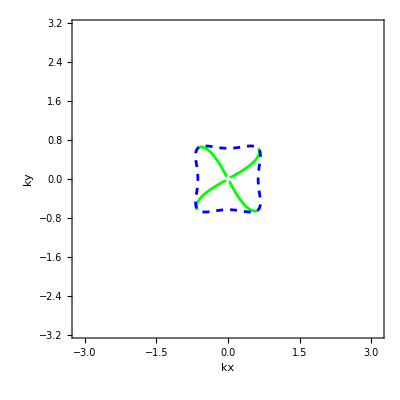

```mathematica
lim=π;mu=-0.4;i=1;
ar1=Quiet[ContourPlot[1/4 (2+ky^2 (-2-1/kz^2)-2 kz^2-kz^2/ky^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[ky/(2 kz)-kz/(2 ky)]>0 ],PlotLegends->Automatic,Contours->10]];
ar2=Quiet[ContourPlot[1/4 (-2+ky^2 (2+1/kz^2)+2 kz^2+kz^2/ky^2)==mu,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{kx,ky},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[ky/(2 kz)+kz/(2 ky)]>0 ],PlotLegends->Automatic,Contours->10]];
(*****)
kx=0;
fs=ContourPlot[kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))==mu^2,{ky,-lim,lim},{kz,-lim,lim},FrameLabel->{kx,ky},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[ar1,ar2,fs]
Clear[kx,α];
```

## FA 2: k1 surface

```mathematica
{ddx,ddy,ddz}
ddx sxψ+ddy syψ+ddz szψ/.kx->-ⅈ Dx//FullSimplify
```

{2 √3 kx ky,kx^2+ky^2-kz^2,√3 (kx-ky) (kx+ky) kz}

-2 ⅈ √3 Dx ky sxψ-kz^2 syψ+ky^2 (syψ-√3 kz szψ)-Dx^2 (syψ+√3 kz szψ)

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2};
ψdag={1,a1-ⅈ a2};
prod=-ⅈ FullSimplify[-2 ⅈ √3  ky ψdag.(sx.ψ)-2ⅈ κi ψdag.(sy.ψ+√3 kz sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1](*{√3 (-1+a1^2+a2^2) ky kz,0}*)
```

{-4 √3 a1 ky,0}

```mathematica
Clear[ψ,eq,eqn,solu];
ψ={1,ⅈ };eq=(* -2 ⅈ √3 Dx ky sxψ-kz^2 syψ+ky^2 (syψ-√3 kz szψ)-Dx^2 (syψ+√3 kz szψ)*)2FullSimplify[-2 ⅈ √3  ky (-κ)sx.ψ-kz^2 sy.ψ+ky^2 (sy.ψ-√3 kz sz.ψ)-κ^2 (sy.ψ+√3 kz sz.ψ)-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu[ky_,kz_]=FullSimplify[Solve[ eqn[[1]]==0  && eqn[[2]]==0  && eqn[[3]]==0 && eqn[[4]]==0 && κr≠0,{en,κr}],ass]
Clear[ky,α];
```

{-2 (en-ky^2+kz^2+2 √3 ky κr+κr^2+√3 kz (ky^2+κr^2)),0,0,2 (-en+ky^2-kz^2+2 √3 ky κr-κr^2+√3 kz (ky^2+κr^2))}

{{en→-(kz^4-2 ky^2 (-1+kz^2)+2 ky √(1-kz^2) Abs[ky])/kz^2,κr→-(ky+√(1-kz^2) Abs[ky])/kz},{en→(-kz^4+2 ky^2 (-1+kz^2)+2 ky √(1-kz^2) Abs[ky])/kz^2,κr→(-ky+√(1-kz^2) Abs[ky])/kz}}

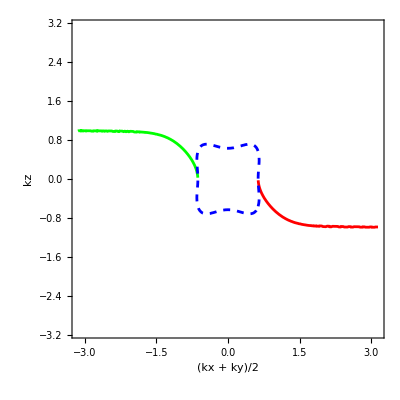

```mathematica
lim=π;mu=0.4;i=1;
ar1=Quiet[ContourPlot[-(kz^4-2 ky^2 (-1+kz^2)+2 ky √(1-kz^2) Abs[ky])/kz^2==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{ky,kz,z},Chop[-(ky+√(1-kz^2) Abs[ky])/kz]>0 ],PlotLegends->Automatic,Contours->10]];
ar2=Quiet[ContourPlot[(-kz^4+2 ky^2 (-1+kz^2)+2 ky √(1-kz^2) Abs[ky])/kz^2==mu,{ky,-lim,lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{ky,kz,z},Chop[(-ky+√(1-kz^2) Abs[ky])/kz]>0 ],PlotLegends->Automatic,Contours->10]];
(*** {k1->(kx+ky)/2,k2->(kx-ky)/2} **)
kx=0;
fs=ContourPlot[kx^4+14 kx^2 ky^2+ky^4-2 kx^2 kz^2+3 kx^4 kz^2-2 ky^2 kz^2-6 kx^2 ky^2 kz^2+3 ky^4 kz^2+kz^4==mu^2,{ky,-lim,lim},{kz,-lim,lim},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[{ar1,ar2,fs},FrameLabel->{"(kx + ky)/2","kz"}]
Clear[kx,α];
```

## FA 2: k2 surface

```mathematica
{ddx,ddy,ddz}
ddx sxψ+ddy syψ+ddz szψ/.ky->-ⅈ Dy//FullSimplify
```

{2 √3 kx ky,kx^2+ky^2-kz^2,√3 (kx-ky) (kx+ky) kz}

-2 ⅈ √3 Dy kx sxψ-kz^2 syψ+Dy^2 (-syψ+√3 kz szψ)+kx^2 (syψ+√3 kz szψ)

```mathematica
Clear[eq0,sol,M,cosa,sina,κ,κr,κi,a,c1,c2];
κi=0;
κ=κr+ⅈ κi;
ψ={1,a1+ⅈ a2};
ψdag={1,a1-ⅈ a2};
prod=-ⅈ FullSimplify[-2 ⅈ √3  kx ψdag. (sx.ψ)+2ⅈ κ ψdag.(-sy.ψ+√3 kz sz.ψ),ass];
eq0=Flatten[FullSimplify[ComplexExpand[ReIm[prod]],ass],1](*{√3 (-1+a1^2+a2^2) ky kz,0}*)
```

{-2 ((2 a2-√3 kz) κr+√3 (2 a1 kx+(a1^2+a2^2) kz κr)),0}

```mathematica
Clear[eq,eqn,solu];
eq=(* -2 ⅈ √3 Dy kx sxψ-kz^2 syψ+Dy^2 (-syψ+√3 kz szψ)+kx^2 (syψ+√3 kz szψ) *)2FullSimplify[-2 ⅈ √3 (-κ) kx sx.ψ-kz^2 sy.ψ+κ^2 (-sy.ψ+√3 kz sz.ψ)+kx^2 (sy.ψ+√3 kz sz.ψ)-en id.ψ,ass];
eqn=Flatten[FullSimplify[ComplexExpand[ReIm[eq]],ass],1]
solu=FullSimplify[Solve[ eq0[[1]]==0 &&eqn[[1]]==0  && eqn[[2]]==0  && eqn[[3]]==0 && eqn[[4]]==0 && κr≠0,{en,κr,a1,a2}],ass];
sol={en,κr}/.solu
Clear[ky,α];
```

{-2 (en-√3 kz (kx^2+κr^2)+a2 (-kx^2+kz^2+2 √3 kx κr+κr^2)),2 a1 (-kx^2+kz^2+2 √3 kx κr+κr^2),-2 a1 (en+√3 kz (kx^2+κr^2)),-2 (-kx^2+kz^2-2 √3 kx κr+κr^2+a2 (en+√3 kz (kx^2+κr^2)))}

{{(kz (-2 kx^2+kz^2) √((-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)) (3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]))/(kx kz^2+kx^3 (-1+3 kz^2)),-√((-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2))},{(kz (2 kx^2-kz^2) √((-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)) (3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]))/(kx kz^2+kx^3 (-1+3 kz^2)),√((-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2))},{(kz (2 kx^2-kz^2) (-3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]) √((-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)))/(kx kz^2+kx^3 (-1+3 kz^2)),-√((-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2))},{(kz (-2 kx^2+kz^2) (-3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]) √((-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)))/(kx kz^2+kx^3 (-1+3 kz^2)),√((-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2))}}

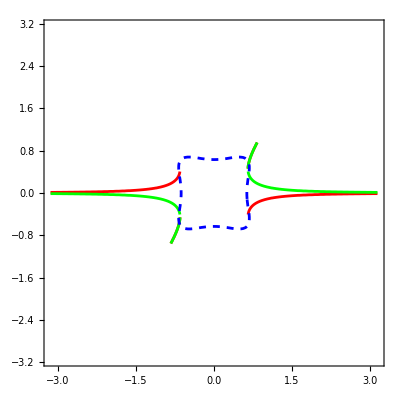

```mathematica
lim=π;mu=0.4;i=1;
ar4=Quiet[ContourPlot[(kz (-2 kx^2+kz^2) (-3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]) √((-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)))/(kx kz^2+kx^3 (-1+3 kz^2))==mu,{kx,-lim,lim},{kz,-lim,lim},ContourStyle->Green,RegionFunction->Function[{kx,kz,z},Chop[-kz^2+kx^2 (7-3 kz^2)+2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]]>0  && -3 kz^2+kx^2 (12-9 kz^2)>0],PlotLegends->Automatic,Contours->10]];
ar3=Quiet[ContourPlot[(kz (2 kx^2-kz^2) √((-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx])/(1+3 kz^2)) (3 kx^2+√(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]))/(kx kz^2+kx^3 (-1+3 kz^2))==mu,{kx,-lim,lim},{kz,-lim,lim},ContourStyle->Red,RegionFunction->Function[{kx,kz,z},Chop[-kz^2+kx^2 (7-3 kz^2)-2 √(-3 kz^2+kx^2 (12-9 kz^2)) Abs[kx]]>0  && -3 kz^2+kx^2 (12-9 kz^2)>0],PlotLegends->Automatic,Contours->10]];
(*** {k1->(kx+ky)/2,k2->(kx-ky)/2} **)
ky=0;
fs=ContourPlot[kx^4+ky^4-ky^2 kz^2+kz^4+kx^2 (-kz^2+ky^2 (-1+3 kz^2))==mu^2,{kx,-lim,lim},{kz,-lim,lim},FrameLabel->{"(kx + ky)/2","(kx - ky)/2"},Contours->20,ContourStyle->{Directive[Red,Dashed],Directive[Blue,Dashed]}];
Show[ar3,ar4,fs]
Clear[kx,ky,α];
```